## Definitions

```mathematica
(*Solutions for incoming momentum p and outgoing momentum q in the CM frame of the 2->2 process*)
psoll=p/.Solve[√(p^2+mp^2)+p==√s,p][[1]]//Quiet;
qsoll=q/.Solve[√(q^2+mp^2)+√(q^2+mX^2)==√s,q][[2]]//Quiet;
(*Here and below, t == -Subscript[t, p] for 2->2 process γ+p->X+p*)
tcosθ[s_,mp_,mX_,cosθ_]=-Refine[2*mp^2-2*(√((qsoll^2+mp^2)//Simplify)*√((psoll^2+mp^2)//Simplify)-psoll*qsoll*cosθ),s-mX^2+mp^2>0&&s>0&&mp>0]//Simplify;
{tmin[s_,mp_,mX_],tmax[s_,mp_,mX_]}=tcosθ[s,mp,mX,#]&/@{1,-1}//Simplify;
tpMin[s_,mp_,mX_]=Module[{L=Sqrt[λKallen[s,mp^2,mX^2]]},4 mX^4 mp^2/((s-mp^2-mX^2+L) (s+mX^2-mp^2+L))];
If[(tmin[s,mp,mX]-tpMin[s,mp,mX]//Simplify)===0,tmin[s_,mp_,mX_]=tpMin[s,mp,mX]];
cosθCMt[s_,mp_,mX_,t_]=cosθ/.Solve[tcosθ[s,mp,mX,cosθ]==t,cosθ][[1]]//Simplify;
(*Pre-factor # in dσ/dcos(θ) = #×OverBar[|M|^2]*)
σfluxFactor=2Pi*(1/(4*Refine[(psoll*√((psoll^2+mp^2)//Simplify)+psoll^2)//Simplify,s>0&&mp>0]//Simplify))qsoll/((2Pi)^2*4 √s);
(*Scalar products replacements*)
scalarProductsRepl2to2=Refine[{ScalarProduct[pp,pγ]->(s-mp^2)/2,ScalarProduct[pppr,pγ]->psoll*√((qsoll^2+mp^2)//Simplify)+psoll*qsoll*cosθ,ScalarProduct[pp,pppr]->√((qsoll^2+mp^2)//Simplify)*√((psoll^2+mp^2)//Simplify)-psoll*qsoll*cosθ,ScalarProduct[pp,pp]->mp^2,ScalarProduct[pppr,pppr]->mp^2,ScalarProduct[pγ,pγ]->0,ScalarProduct[pX,pX]->mX^2,ScalarProduct[pp,pX]->√((qsoll^2+mX^2)//Simplify)*√((psoll^2+mp^2)//Simplify)+psoll*qsoll*cosθ,ScalarProduct[pγ,pX]->√((qsoll^2+mX^2)//Simplify)*psoll-psoll*qsoll*cosθ,ScalarProduct[pppr,pX]->√((qsoll^2+mX^2)//Simplify)*√((qsoll^2+mp^2)//Simplify)+qsoll^2}//Simplify,s-mX^2+mp^2>0&&s>0&&mp>0&&mX>0&&-mp^2+mX^2+s>0]//Simplify;
polγ[μ_]=PolarizationVector[pγ,μ];
polV[μ_]=PolarizationVector[pX,μ];
momγ[μ_]=FV[pγ,μ];
momV[μ_]=FV[pX,μ];
ubarppr=SpinorUBar[pppr,mp];
up=SpinorU[pp,mp];
replIndices={μ->μC,ν->νC,α->αC,β->βC,κ->κC,δ->δC,λ->λC,σ->σC,ρ->ρC};
squaredMphotoProd[M1_,M2_,ifV_,ruleM1_:{},ruleM2_:{}]:=Module[{Mel2},
Mel2=If[M1===M2,M1*(ComplexConjugate[M1]/.replIndices/.ruleM1),M1*(ComplexConjugate[M2]/.replIndices/.ruleM2)+M2*(ComplexConjugate[M1]/.replIndices/.ruleM1)];
If[ifV,Mel2=DoPolarizationSums[Mel2,pX]];
1/4 FermionSpinSum[DoPolarizationSums[Mel2,pγ,0]]/.{DiracTrace->TR}//ExpandScalarProduct//Contract//Quiet
];
MsquaredPhotoXInsertedKinematics[M1_,M2_,ifV_,ruleM1_:{},ruleM2_:{}]:=With[{M=squaredMphotoProd[M1,M2,ifV,ruleM1,ruleM2]},
M/.scalarProductsRepl2to2//Simplify
]
dσdtXphotoTemp[M2_]:=Refine[-σfluxFactor*D[cosθCMt[s,mp,mX,t],t]*(M2/.{cosθ->cosθCMt[s,mp,mX,t]}),s>0&&t>0&&mX>0]
```

```mathematica
Δ
```

Δ

## Production of pseudoscalar particles

## Calculating squared matrix elements

```mathematica
JvecHadrPV=I*gγPV*gVpp*LeviCivita[μ,ν,α,β]*momγ[ν]*FV[pp-pppr,α]*ubarppr.(GA[β](1+κV)-κV/(2mp)*(FV[pp+pppr,β])).SpinorU[pp,mp]*ReggeV//Contract;
ruleVprodPV={Reggeρ->ReggeρStar,Reggeω->ReggeωStar};
MepToepPρ=JvecHadrPV*polγ[μ]/.{ReggeV->Reggeρ,κV->κρ,gγPV->gγPρ,gVpp->gρpp}//ExpandScalarProduct//Contract//Simplify;
MepToepPω=JvecHadrPV*polγ[μ]/.{ReggeV->Reggeω,κV->κω,gγPV->gγPω,gVpp->gωpp}//ExpandScalarProduct//Contract//Simplify;
MsquaredPprodPhotoV[s_,αEM_,cosθ_,mp_,mX_,gρpp_,κρ_,gγPρ_,Reggeρ_,ReggeρStar_,gωpp_,κω_,gγPω_,Reggeω_,ReggeωStar_]=MsquaredPhotoXInsertedKinematics[MepToepPρ,MepToepPρ,False,ruleVprodPV,ruleVprodPV]+MsquaredPhotoXInsertedKinematics[MepToepPω,MepToepPω,False,ruleVprodPV,ruleVprodPV]+MsquaredPhotoXInsertedKinematics[MepToepPρ,MepToepPω,False,ruleVprodPV,ruleVprodPV];
```

## Differential cross-section (numeric)

```mathematica
Do[
replFactors={Reggeρ->ReggeizedPropagatorρ[s,-t,P],ReggeρStar->ReggeizedPropagatorρStar[s,-t,P],Reggeω->ReggeizedPropagatorω[s,-t,P],ReggeωStar->ReggeizedPropagatorωStar[s,-t,P]};
replNum={mX->MASS[P],αEM->αEMval,mp->mpval,κρ->(*κVval["ρ^0"]*)4.2,κω->κVval["ω"],gρpp->gVNNval["ρ^0"],gωpp->gVNNval["ω"],gγPρ->gPVγ[P,"ρ^0"],gγPω->gPVγ[P,"ω"]};
dσdtPphotoNum[s_,t_,P]= GeVm2Tob*dσdtXphotoTemp[MsquaredPprodPhotoV[s,αEM,cosθ,mp,mX,gρpp,κρ,gγPρ,Reggeρ,ReggeρStar,gωpp,κω,gγPω,Reggeω,ReggeωStar]]/.replFactors/.replNum;
,{P,{"π^0","η","η'"}}]
```

### Validation

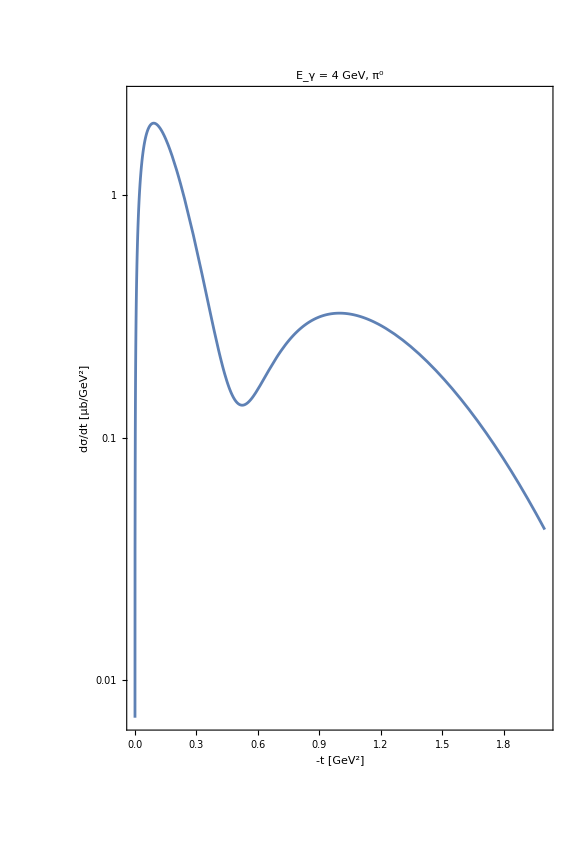
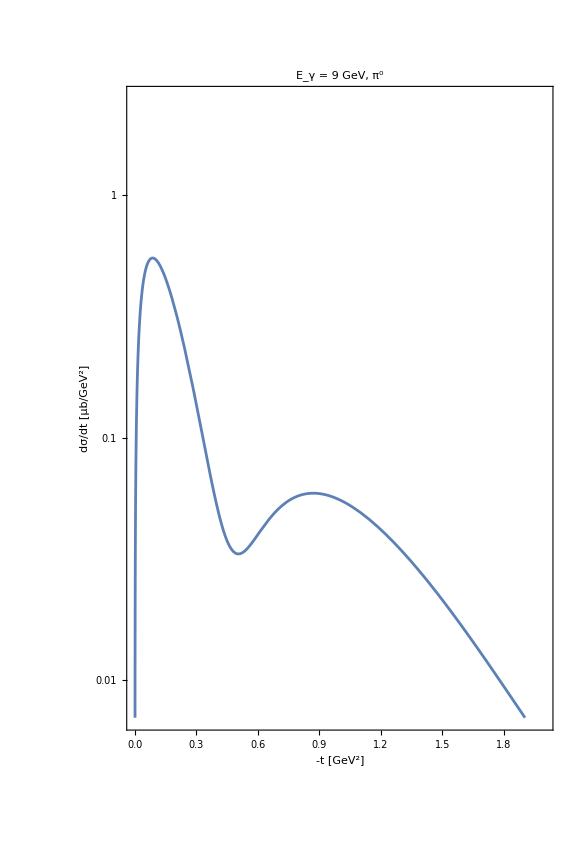
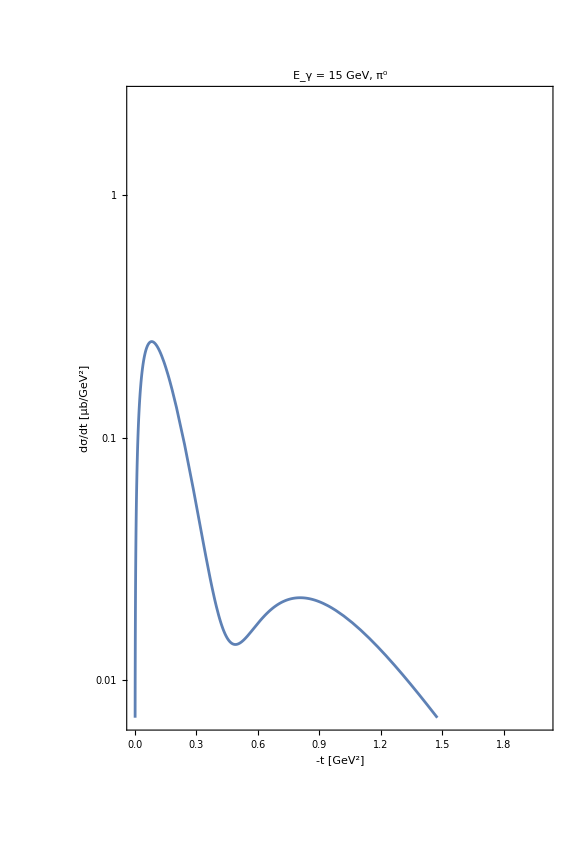

```mathematica
plott[Eγ_,P_,xmax_,ymin_,ymax_,aspRat_]:=With[{s=mpval^2+2*mpval*Eγ},
LogPlot[Re[10^6 dσdtPphotoNum[s,t,P]],{t,0.,2.},Frame->True,ImageSize->Large,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],PlotRange->{{0.,xmax},{ymin,ymax}},FrameLabel->{"-t [GeV^2]","dσ/dt [μb/GeV^2]"},PlotLabel->Style[Row[{"E_γ = ",Eγ," GeV, ",P}],20,Black,FontFamily->"Palatino"],AspectRatio->aspRat]
]
plott[#,"π^0",2.,7*10^-3.,2.5,1.5]&/@{4,9,15}
```

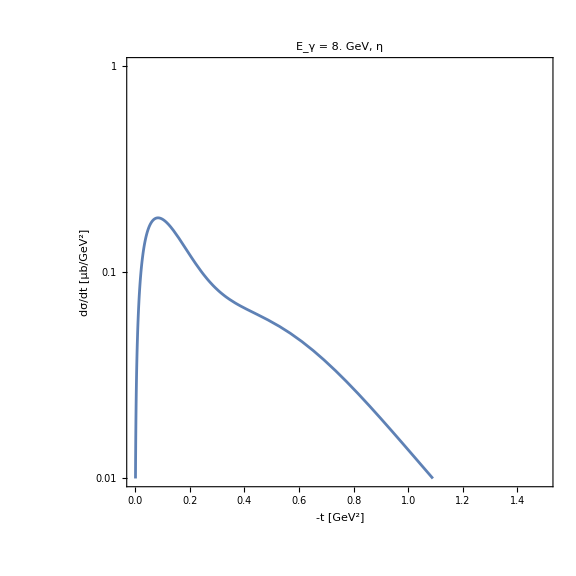

```mathematica
plott[8.,"η",1.5,10^-2.,1.,1]
```

### Comparison vs Kaskulov

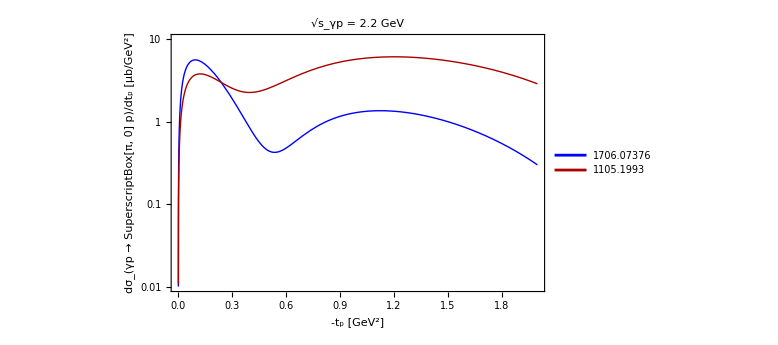

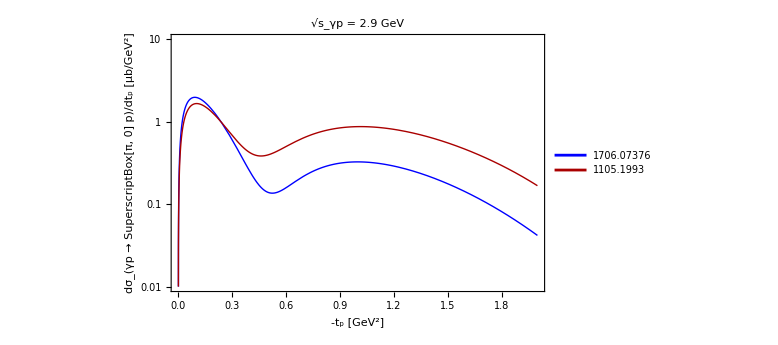

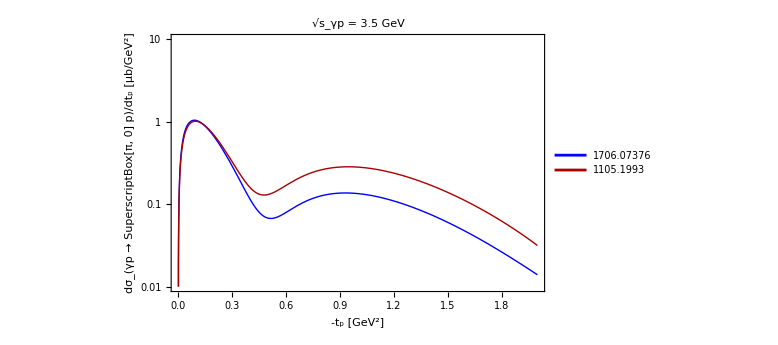

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\pi0-prod-Kasheverov-vs-Kaskulov-Egamma=2-GeV.pdf

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\pi0-prod-Kasheverov-vs-Kaskulov-Egamma=4-GeV.pdf

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\pi0-prod-Kasheverov-vs-Kaskulov-Egamma=6-GeV.pdf

```mathematica
dataKaskulov[s_,t_]=Import[FileNameJoin[{dir["datasets"],"dsigmadtKaskulov.mx"}],"MX"]/.{λ->0};
plotVsKaskulov[Eγ_,xmax_,ymin_,ymax_,aspRat_]:=With[{s=mpval^2+2*mpval*Eγ},
label=If[√s==IntegerPart[√s],√s,Round[√s,0.1]];
LogPlot[{Re[10^6 dσdtPphotoNum[s,t,"π^0"]],Re[0.8*10^6 dataKaskulov[s,t][[-1]]]},{t,0.,2.},Frame->True,ImageSize->Large,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],PlotRange->{{0.,xmax},{ymin,ymax}},FrameLabel->{"-t_p [GeV^2]","dσ_(γp → SuperscriptBox[π, 0] p)/dt_p [μb/GeV^2]"},PlotLabel->Style[Row[{"√s_γp = ",label," GeV"}],20,Black,FontFamily->"Palatino"],AspectRatio->aspRat,PlotStyle->{{Thick,Blue},{Thick,Darker@Red}},PlotLegends->Placed[Style[Row[{#}],22,Black,FontFamily->"Palatino"]&/@{"1706.07376","1105.1993"}, {0.8,0.1}],ImagePadding->{{Automatic,Automatic}, {Automatic, 0.6}}]
]
pt1=plotVsKaskulov[2.,2,10^-2.,10,0.6]
pt2=plotVsKaskulov[4.,2,10^-2.,10,0.6]
pt3=plotVsKaskulov[6.,2,10^-2.,10,0.6]
Export[FileNameJoin[{dir["plots"],"pi0-prod-Kasheverov-vs-Kaskulov-Egamma=2-GeV.pdf"}],pt1]
Export[FileNameJoin[{dir["plots"],"pi0-prod-Kasheverov-vs-Kaskulov-Egamma=4-GeV.pdf"}],pt2]
Export[FileNameJoin[{dir["plots"],"pi0-prod-Kasheverov-vs-Kaskulov-Egamma=6-GeV.pdf"}],pt3]
```

## EPA

```mathematica
xminEPAabs[mX_,mp_,Ep_,Ee_]=((mX+mp)^2-mp^2)/(4*Ee*Ep);
xmaxEPAabs[me_,Ee_]=Min[0.9,1-me/(2Ee)];
Q2minEPAx[x_,me_]=(x^2*me^2)/(1-x);
Q2maxEPAabs=10.;
Q2maxEPAx[x_,Ee_]=Min[4*Ee^2*(1-x),Q2maxEPAabs];
xminEPAQ2[mX_,mp_,Ep_,Ee_]=((mX+mp)^2-mp^2)/(4*Ee*Ep);
xmaxEPAQ2[mX_,me_,Q2_,Ee_]=Min[(*Q2/(2 me^2) (Sqrt[1+4 me^2/Q2]-1)*)2/(√(1+4 me^2/Q2)+1),1-Q2/(4*Ee^2)];
Q2minEPAabs[mX_,mp_,me_,Ep_,Ee_]=Q2minEPAx[x,me]/. {x->xminEPAabs[mX,mp,Ep,Ee]}//Simplify;

(*Finally,the cos(Subscript[θ,e'])-x space*)
Q2xθepr[Ee_,me_,x_,θepr_]=Q2minEPAx[x,me]+2*Ee^2 (1-x)*(1-Cos[θepr]);
JacobianxQ2toxθepr[Ee_,x_,θepr_]=D[Q2xθepr[Ee,me,x,θepr],θepr];
xminEPAθepr[mX_,mp_,θepr_,Ep_,Ee_]=Max[xminEPAabs[mX,mp,Ep,Ee],1-If[θepr>10^-4.,Evaluate[Q2maxEPAabs/(2 Ee^2 (1-Cos[θepr]))],Evaluate[Q2maxEPAabs/(Ee^2*θepr^2)]]];
xmaxEPAθepr[mX_,me_,θepr_,Ee_]=Min[xmaxEPAabs[me,Ee],If[θepr>10^-4,Evaluate[1/(1+me/(Ee Sqrt[2 (1-Cos[θepr])]))],Evaluate[1/(1+me/(Ee*θepr))]]];
θeprMaxEPAabs[mX_,mp_,me_,Ep_,Ee_]=ArcCos[Max[-1,1-Q2maxEPAabs/(2*Ee^2*(1-xmaxEPAabs[me,Ee]))]];

θeprMinEPAabs[mX_,mp_,me_,Ep_,Ee_]=ArcCos[With[{xmin=xminEPAabs[mX,mp,Ep,Ee]},Min[1,1-(xmin^2*me^2)/(2*Ee^2*(1-xmin)^2)]]];
(*EPA fluxes*)
EPAfluxInQ2x[x_,Q2_,αEM_,me_,FphotoToElectro_]=FphotoToElectro^2*αEM/(2Pi)1/Q2 1/x((1+(1-x)^2)-(2*(1-x)) Q2minEPAx[x,me]/Q2);
sInxEPA[mp_,Ep_,Ee_,x_]=(mp^2+4*Ep*x*Ee);
(*______________________________*)
(*Differential cross-sections*)
(*d^3 σ/dxdQ^2d|Subscript[t, p]|*)
d2σdQ2dxdtEPA[Q2_?NumericQ,x_?NumericQ,t_?NumericQ,Ee_?NumericQ,Ep_?NumericQ,pt_]:=EPAfluxInQ2x[x,Q2,αEMval,meval,FphotoToElectroP[pt,Q2,MASS[pt]]]*dσdtPphotoNum[sInxEPA[mpval,Ep,Ee,x],t,pt];
(*d^2 σ/dxdQ^2*)
dσdQ2dxEPA[Q2_,x_,Ee_,Ep_,pt_]:=If[(*Q2minEPAabs[mP[pt],mpval,meval,Ep,Ee]<Q2<Q2maxEPAabs*)xminEPAabs[mP[pt],mpval,Ep,Ee]<x<xmaxEPAabs[meval,Ee],If[(*xminEPAQ2[mP[pt],mpval,Ep,Ee]<x<xmaxEPAQ2[mP[pt],meval,Q2,Ee]*)Q2minEPAx[x,meval]<Q2<Q2maxEPAx[x,Ee],NIntegrate[d2σdQ2dxdtEPA[Q2,x,Exp[t],Ee,Ep,pt]* Exp[t],{t,Log[tmin[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"],0.],0.]
(*dσ/dx*)
dσdxEPA[x_,Ee_,Ep_,Q2min_,Q2max_,pt_]:=If[xminEPAabs[MASS[pt],mpval,Ep,Ee]<x<xmaxEPAabs[meval,Ee]&&Max[Q2minEPAx[x,meval],Q2min]<Min[Q2max,Q2maxEPAx[x,Ee],Q2maxEPAabs],NIntegrate[d2σdQ2dxdtEPA[Exp[Q2],x,Exp[t],Ee,Ep,pt] Exp[t+Q2],{Q2,Log[Max[Q2minEPAx[x,meval],Q2min]],Log[Min[Q2max,Q2maxEPAx[x,Ee],Q2maxEPAabs]]},{t,Log[tmin[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"],0.]
(*dσ/dQ^2*)
dσdQ2EPA[Q2_,Ee_,Ep_,pt_]:=If[Q2minEPAabs[mP[pt],mpval,meval,Ep,Ee]<Q2<Q2maxEPAabs&&xminEPAQ2[mP[pt],mpval,Ep,Ee]<xmaxEPAQ2[mP[pt],meval,Q2,Ee],NIntegrate[d2σdQ2dxdtEPA[Q2,Exp[x],Exp[t],Ee,Ep,pt] Exp[t+x],{x,Log[xminEPAQ2[mP[pt],mpval,Ep,Ee]],Log[xmaxEPAQ2[mP[pt],meval,Q2,Ee]]},{t,Log[tmin[sInxEPA[mpval,Ep,Ee,Exp[x]],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,Exp[x]],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"],0.]
(*dσ/Subscript[dθ, e']*)
dσdθeprEPA[θepr_,Ee_,Ep_,pt_]:=If[θeprMinEPAabs[mP[pt],mpval,meval,Ep,Ee]<θepr<θeprMaxEPAabs[mP[pt],mpval,meval,Ep,Ee],If[xminEPAθepr[mP[pt],mpval,θepr,Ep,Ee]<xmaxEPAθepr[mP[pt],meval,θepr,Ee],NIntegrate[JacobianxQ2toxθepr[Ee,Exp[x],θepr]*d2σdQ2dxdtEPA[Q2xθepr[Ee,meval,Exp[x],θepr],Exp[x],Exp[t],Ee,Ep,pt] Exp[t+x],{x,Log[xminEPAθepr[mP[pt],mpval,θepr,Ep,Ee]],Log[xmaxEPAθepr[mP[pt],meval,θepr,Ee]]},{t,Log[tmin[sInxEPA[mpval,Ep,Ee,Exp[x]],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,Exp[x]],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"],0.],0.]
(*dσdθeprdxEPA[θepr_,x_,Ee_,Ep_,pt_]:=If[θeprMinEPAabs[mP[pt],mpval,meval,Ep,Ee]<θepr<θeprMaxEPAabs[mP[pt],mpval,meval,Ep,Ee],If[xminEPAθepr[mP[pt],mpval,θepr,Ep,Ee]<x<xmaxEPAθepr[mP[pt],meval,θepr,Ee],NIntegrate[JacobianxQ2toxθepr[Ee,x,θepr]*d2σdQ2dxdtEPA[Q2xθepr[Ee,meval,x,θepr],x,Exp[t],Ee,Ep,pt] Exp[t],{t,Log[tmin[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"],0.],0.]*)
(*_____________________________________________________________________*)
(*dσ/dx - here assuming the unit photo-to-electro form-factor*)
EPAfluxInx[x_,Ee_,Ep_,mX_,me_,mp_,αEM_,Q2min_,Q2max_]=(With[{f=Integrate[EPAfluxInQ2x[x,Q2,αEM,me,1],Q2]},(f/. {Q2->Min[Q2max,Q2maxEPAx[x,Ee],Q2maxEPAabs]})-(f/. {Q2->Max[Q2minEPAx[x,me],Q2min]})]//Simplify);
d2σdxdtEPAunitF[x_?NumericQ,t_?NumericQ,Ee_?NumericQ,Ep_?NumericQ,Q2min_?NumericQ,Q2max_?NumericQ,pt_]:=EPAfluxInx[x,Ee,Ep,mP[pt],meval,mpval,αEMval,Q2min,Q2max]*dσdtPphotoNum[sInxEPA[mpval,Ep,Ee,x],t,0,pt];
dσdxEPAunitF[x_,Ee_,Ep_,Q2min_,Q2max_,pt_]:=NIntegrate[d2σdxdtEPAunitF[x,Exp[t],Ee,Ep,Q2min,Q2max,pt] Exp[t],{t,Log[tmin[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]],Log[tmax[sInxEPA[mpval,Ep,Ee,x],mpval,mP[pt]]]},Method->"AdaptiveMonteCarlo"];
(*_____________________________________________________________________*)
```

## Various plots

### Importing the 2→3 data and some definitions

```mathematica
NeventsTest=5*10^6;
energylist={"275×18","100×10","41×5"};
{σ2to3Total,mesonSample,dσdQ22to3analytic}//Clear;
(*If regenerating analytic dσ/dQ^2 by the 2->3 approach*)
ifGeneratedσdQ2ini=False;
(*If generatign the total 2->3 cross-section*)
ifGenerateσ=False;
Print["Generating/importing total cross-section..."];
fileσ=FileNameJoin[{dir["datasets"],"MC calculation","cross-sections-mesons-setups.mx"}];
If[!FileExistsQ[fileσ],ifGenerateσ=True];
If[ifGenerateσ,
ResourceFunction["MonitorProgress"]@Do[
Block[{Ep,Ee,sample},
{Ep,Ee}=energies[setup];
Print[Row[{"Setup ", setup}]];
ResourceFunction["MonitorProgress"]@Do[
BlockFinal[P,mP[P],fatest,Ep,Ee,NeventsTest,mP[P],mpval,Ep,0.,-14.,14.,0.,3.];
σ2to3Total[setup,P]=σtot;
,{P,mesonsP}];
]
,{setup,energylist}];
tabMesonsAll=Flatten[Table[{setup,P,σ2to3Total[setup,P]},{setup,EnergiesConfigurations},{P,mesonsP}],1];
Export[fileσ,tabMesonsAll,"MX"]
,
tabMesonsAll=Import[fileσ,"MX"];
Do[
σ2to3Total[tabMesonsAll[[i]][[1]],tabMesonsAll[[i]][[2]]]=tabMesonsAll[[i]][[3]]
,{i,1,Length[tabMesonsAll]}];
]//AbsoluteTiming
Print["Generating/importing analytic dσ/dQ^2..."]
ResourceFunction["MonitorProgress"]@Do[
Block[{Ep,Ee},
{Ep,Ee}=energies[setup];
ResourceFunction["MonitorProgress"]@Do[
ifGeneratedσdQ2=ifGeneratedσdQ2ini;
fileQ2=FileNameJoin[{dir["datasets"],"Analytic calculation","dsigmadQ2_"<>exportName[setup]<>"_"<>mapMeson[meson]<>".mx"}];
If[!FileExistsQ[fileQ2],ifGeneratedσdQ2=True];
If[ifGeneratedσdQ2,
Module[{gpργ=gPVγ[meson,"ρ^0"],gpωγ=gPVγ[meson,"ω"],gpnn=gPNN[meson]},
dσdQ22to3analytic[setup,meson]=dσPdt1AnalyticTab[meson,mP[meson],fatest,Ep,Ee,"AdaptiveQuasiMonteCarlo"];
Export[fileQ2,dσdQ22to3analytic[setup,meson],"MX"]
]
,
dσdQ22to3analytic[setup,meson]=Import[fileQ2,"MX"]
];
Block[{Q2min=Min[dσdQ22to3analytic[setup,meson][[All,1]]],Q2max=Max[dσdQ22to3analytic[setup,meson][[All,1]]]},
dσdQ22to3analyticInt[setup,meson,Q2_]=If[Min[dσdQ22to3analytic[setup,meson][[All,1]]]<=Q2<=Max[dσdQ22to3analytic[setup,meson][[All,1]]],Evaluate[Interpolation[{Log[#[[1]]],Log[Max[#[[2]],10^-90.]]}&/@dσdQ22to3analytic[setup,meson],InterpolationOrder->1][Log[Q2]]//Exp],0.];
σ2to3Q2cut[setup,meson]=NIntegrate[dσdQ22to3analyticInt[setup,meson,Exp[Q2]]Exp[Q2],{Q2,Log[10^-3.],Log[0.1]},Method->"InterpolationPointsSubdivision"]//Quiet
]
,{meson,mesonsP}]
]
,{setup,energylist}]//AbsoluteTiming
Print["Importing existing MC samples..."]
Do[
filesample=FileNameJoin[{dir["datasets"],"Samples","Distribution_"<>exportName[setup]<>"_"<>mapMeson[P]<>"_No-cuts.mx"}];
If[FileExistsQ[filesample],
mesonSample[setup,P]=Import[FileNameJoin[{dir["datasets"],"Samples","Distribution_"<>exportName[setup]<>"_"<>mapMeson[P]<>"_No-cuts.mx"}],"MX"];
]
,{P,mesonsP},{setup,energylist}];//AbsoluteTiming
Print["Done"]
```

Generating/importing total cross-section...

{0.0117992,Null}

Generating/importing analytic dσ/dQ^2...

{2.0544,Null}

Importing existing MC samples...

{4.95504,Null}

Done

#### Definitions

```mathematica
dataToQ2xyComp=Hold@Compile[{{data,_Real,1},{Ep,_Real},{Ee,_Real}},Module[{s=sep[Ep,Ee,mpval,meval],Eepr=data[[indexFinEepr]],Q2=-data[[indexFint1]],s2=data[[indexFins2]]},
{Q2,(Ee-Eepr)/Ee,(s2-mpval^2+Q2)/(s-mpval^2-meval^2)}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleOwn[{mpval,meval,indexFinEepr,indexFint1,indexFins2}]/.ruleDown[{sep}]//ReleaseHold;
checkIfCompiled[dataToQ2xyComp]
selectorPositivex=Compile[{{datta,_Real,2}},Select[datta,#[[2]]>0&],CompilationTarget->"C",RuntimeOptions->"Speed"];
checkIfCompiled[selectorPositivex]
selectorQ2comp=Compile[{{data,_Real,2},{Q2min,_Real},{Q2max,_Real},{indexQ2,_Integer}},Select[data,Q2min<=#[[indexQ2]]<=Q2max&],CompilationTarget->"C",RuntimeOptions->"Speed"];
checkIfCompiled[selectorQ2comp]
```

{True,{}}

{True,{}}

{True,{}}

### dσ/dy and dσ/dQ^2

#### Specifying setup

```mathematica
setupSel="100×10";
{Epv,Eev}=energies[setupSel];
ptsel="η'";
ptsel2="π^0";
```

#### Preparing data

EPA

```mathematica
Q2minWindow=1.;
Q2maxWindow=4.;
ResourceFunction["MonitorProgress"]@Do[
ttttEPAfullQ2[pt]=ParallelTable[{10^x,dσdxEPA[10^x,Eev,Epv,0.,100.,pt]//Quiet},{x,Log10[xminEPAabs[mP[pt],mpval,Epv,Eev]],Log10[xmaxEPAabs[meval,Eev]],0.025}];
ttttEPAconstrainedQ2[pt]={#[[1]],If[Im[#[[2]]]!=0.,10^-90.,#[[2]]]}&/@ParallelTable[{10^x,dσdxEPA[10^x,Eev,Epv,Q2minWindow,Q2maxWindow,pt]//Quiet},{x,Log10[xminEPAabs[mP[pt],mpval,Epv,Eev]],Log10[xmaxEPAabs[meval,Eev]],0.01}];
ttttQ2EPA[pt]=ParallelTable[{10^x,dσdQ2EPA[10^x,Eev,Epv,pt]//Quiet},{x,Log10[Q2minEPAabs[mP[pt],mpval,meval,Epv,Eev]],Log10[Q2maxEPAabs],(Log10[Q2maxEPAabs]-Log10[Q2minEPAabs[mP[pt],mpval,meval,Epv,Eev]])/130}];
,{pt,{ptsel,ptsel2}}]
```

2→3

```mathematica
ResourceFunction["MonitorProgress"]@Do[
dattaFullQ2[pt]=dataToQ2xyComp[mesonSample[setupSel,pt],Epv,Eev];
{tttt2to3FullQ2x[pt],tttt2to3FullQ2y[pt]}=Table[{#[[1]],#[[2]]*σ2to3Total[setupSel,pt]}&/@pdf1Dmaker[dattaFullQ2[pt],i,200],{i,{2,3}}];
dattaConstrainedQ2[pt]=selectorQ2comp[dattaFullQ2[pt],Q2minWindow,Q2maxWindow,1];
{tttt2to3ConstrainedQ2x[pt],tttt2to3ConstrainedQ2y[pt]}=Table[{#[[1]],#[[2]]*σ2to3Total[setupSel,pt]}&/@pdf1Dmaker[dattaConstrainedQ2[pt],i,100],{i,{2,3}}];
dattaFullQ22to3Analytic[pt]=dσdQ22to3analytic[setupSel,pt];
(*Q^2 distribution*)
dattaFullQ22to3MC[pt]={#[[1]],#[[2]]*σ2to3Total[setupSel,pt]}&/@pdf1Dmaker[dattaFullQ2[pt],1,200];//AbsoluteTiming
,{pt,{ptsel,ptsel2}}]
```

#### Plots

dσ/dy

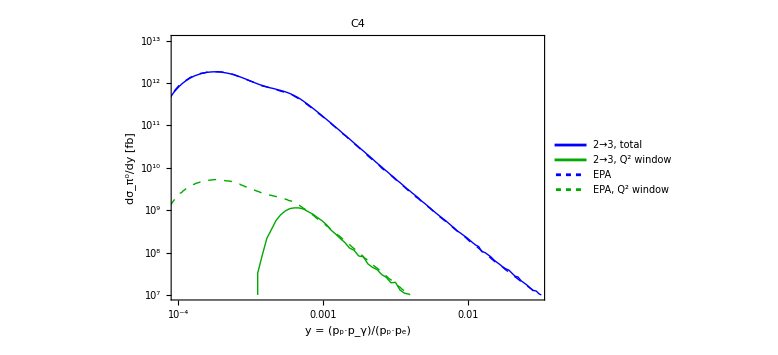
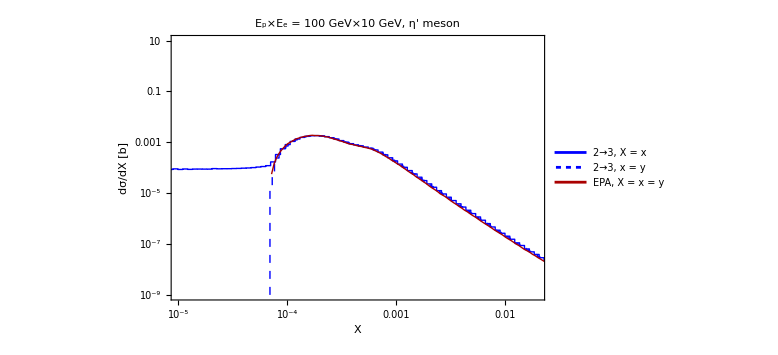

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\dsigmady-EPA-comparison.pdf

```mathematica
epilog={Inset[Framed[Style[Row[{"e p → e p ",X,", ",compactNameConf[setupSel]}],22,Black,FontFamily->"Palatino"],FrameStyle->Directive[Black,Thickness[0.9]],Background->White,FrameMargins->Medium],Scaled[{0.22,0.89}]]};
ptSel=ptsel2;
ptdσdy=ListLogLogPlot[Evaluate[{{#[[1]],btofb*#[[2]]}&/@tttt2to3FullQ2y[ptSel],{#[[1]],btofb*#[[2]]*Length[dattaConstrainedQ2[ptSel]]/Length[dattaFullQ2[ptSel]]}&/@tttt2to3ConstrainedQ2y[ptSel],{#[[1]],btofb*#[[2]]}&/@ttttEPAfullQ2[ptSel],{#[[1]],btofb*#[[2]]}&/@ttttEPAconstrainedQ2[ptSel]}],PlotRange->{{10^-4,0.03},{btofb*10^-8,btofb*0.01}},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],Joined->True,InterpolationOrder->{1,1,1,1},PlotStyle->{{Thick,Blue},{Thick,Darker@Green},{Thick,Blue,Dashing[0.01]},{Thick,Darker@Green,Dashing[0.01]}},FrameLabel->{"y = (p_p·p_γ)/(p_p·p_e)",Row[{Subscript["dσ",ptSel],"/dy [fb]"}]},ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"2→3, total","2→3, Q^2 window","EPA","EPA, Q^2 window"}, {0.75,0.8}],FrameTicks->ticksLogX,PlotLabel->Style[Row[{compactNameConf[setupSel]}],20,Black,FontFamily->"Palatino"],ImagePadding->{{Automatic,Automatic},{Automatic,0.6}}];
ptdσdxdy=ListLogLogPlot[{tttt2to3FullQ2x[ptSel],tttt2to3FullQ2y[ptSel],ttttEPAfullQ2[ptSel]},PlotRange->{{10^-5,0.02},{10^-9,10}},Joined->True,PlotRange->All,FrameLabel->{"X","dσ/dX [b]"},PlotRange->{{5*10^-5,0.03},{10^-9,0.01}},InterpolationOrder->{0,0,1,1},Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],Joined->True,PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.01]},{Thick,Darker@Red},{Thick,Darker@Red,Dashing[0.01]}},ImageSize->Large,PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"2→3, X = x","2→3, x = y","EPA, X = x = y"}, {0.75,0.8}],FrameTicks->ticksLogX,PlotLabel->Style[Row[{"E_p×E_e = ",energies[setupSel][[1]]//IntegerPart," GeV×",energies[setupSel][[2]]//IntegerPart," GeV, ",ptsel," meson"}],20,Black,FontFamily->"Palatino"],ImagePadding->{{Automatic,Automatic},{Automatic,0.6}}];
Style[Row[{ptdσdy,ptdσdxdy}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{dir["plots"],"dsigmady-EPA-comparison.pdf"}],ptdσdy]
```

dσ/dQ^2

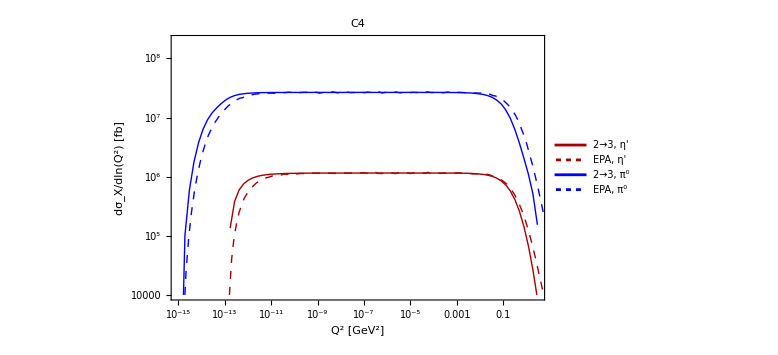
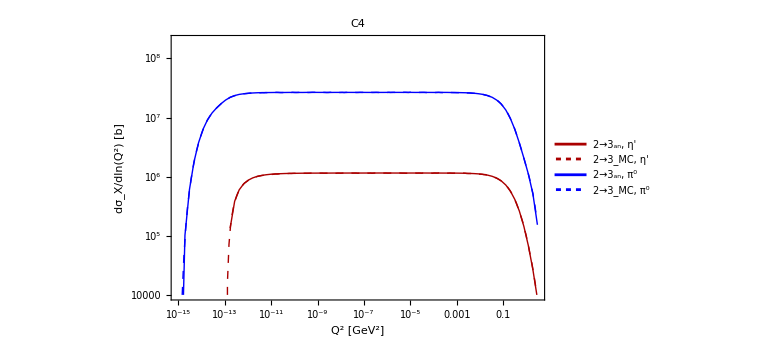

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\dsigmadQ2-EPA-comparison.pdf

```mathematica
plotdσdlnQ21=Module[{dataanalytic,ranges,mesonlist={}},
ListLogLogPlot[Table[{#[[1]],btofb#[[1]]*#[[2]]}&/@tab,{tab,{dattaFullQ22to3Analytic[ptsel],ttttQ2EPA[ptsel],dattaFullQ22to3Analytic[ptsel2],ttttQ2EPA[ptsel2]}}],PlotRange->{{10^-15,3},{btofb*10^-11,btofb*2*10^-7}},Joined->True,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],ImageSize->Large,FrameLabel->{"Q^2 [GeV^2]","dσ_X/dln(Q^2) [fb]"},PlotLabel->Style[Row[{compactNameConf[setupSel]}],20,FontFamily->"Palatino",Black],InterpolationOrder->{1,1,1,1},PlotStyle->{{Thick,Darker@Red},{Thick,Darker@Red,Dashing[0.01]},{Thick,Blue},{Thick,Blue,Dashing[0.01]}},PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{Row[{"2→3, ",ptsel}],Row[{"EPA, ",ptsel}],Row[{"2→3, ",ptsel2}],Row[{ "EPA, ",ptsel2}]},{0.82,0.2}],FrameTicks->ticksLogXrare,ImagePadding->{{Automatic, Automatic}, {Automatic,0.6}}]
];
plotdσdlnQ22=Module[{dataanalytic,ranges,mesonlist={}},
ListLogLogPlot[Table[{#[[1]],btofb#[[1]]*#[[2]]}&/@tab,{tab,{dattaFullQ22to3Analytic[ptsel],dattaFullQ22to3MC[ptsel],dattaFullQ22to3Analytic[ptsel2],dattaFullQ22to3MC[ptsel2]}}],PlotRange->{{10^-15,3},{btofb*10^-11,btofb*2*10^-7}},Joined->True,Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],ImageSize->Large,InterpolationOrder->{1,1,1,1},FrameLabel->{"Q^2 [GeV^2]",Row[{Subscript["dσ","X"],"/dln(Q^2) [b]"}]},PlotLabel->Style[Row[{compactNameConf[setupSel]}],20,FontFamily->"Palatino",Black],PlotStyle->{{Thick,Darker@Red},{Thick,Darker@Red,Dashing[0.01]},{Thick,Blue},{Thick,Blue,Dashing[0.01]}},PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{Row[{"2→3_an, ",ptsel}],Row[{"2→3_MC, ",ptsel}],Row[{"2→3_an, ",ptsel2}],Row[{ "2→3_MC, ",ptsel2}]},{0.85,0.2}],FrameTicks->ticksLogXrare,ImagePadding->{{Automatic, Automatic}, {Automatic,0.6}}]
];
Style[Row[{plotdσdlnQ21,plotdσdlnQ22}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{dir["plots"],"dsigmadQ2-EPA-comparison.pdf"}],plotdσdlnQ21]
```

### dσ/dθ_e'

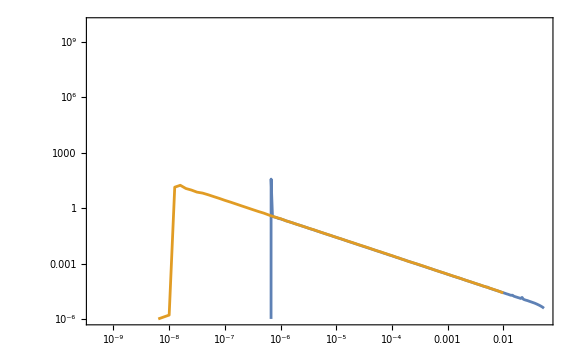

```mathematica
With[{setup="275×18",pt="π^0"},
{Epv,Eev}=energies[setup];
datta=Partition[Pi-ArcCos[mesonSample[setup,pt][[All,indexFincosθepr]]],1];

dσdθeprTabEPA=ParallelTable[{10^x,Max[10^-90.,Re[dσdθeprEPA[10^x,Eev,Epv,pt]]]},{x,-9.,-2.,0.1}];
plot=ListLogLogPlot[{{#[[1]],#[[2]]*σ2to3Total[setup,pt]}&/@pdf1Dmaker[datta,1,200],dσdθeprTabEPA},PlotRange->{{10^-6,0.1},{10^-6,10^10}},Joined->True,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],FrameLabel->{"θ_e' [rad]","dσ/dθ_e' [b/rad]"},PlotLegends->Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"2→3","EPA"},{0.8,0.8}]]
]
```

### d^2 σ/dydQ^2

#### Specifying setup

```mathematica
setupSel="100×10";
{Epv,Eev}=energies[setupSel];
ptsel="η";
```

#### Preparing data

EPA

```mathematica
dσdxdQ2TabEPA=Flatten[ParallelTable[{Q2,x,Max[Re[dσdQ2dxEPA[Q2,x,Eev,Epv,ptsel]],10^-90.]},{Q2,Table[10^x,{x,-17.,0.,0.1}]},{x,Table[10^y,{y,-9.,0.,0.1}]}],{1,2}];//AbsoluteTiming
```

{161.852,Null}

2→3

```mathematica
dattaFullQ2=dataToQ2xyComp[mesonSample[setupSel,ptsel],Epv,Eev];//AbsoluteTiming
{pdfSimx,pdfSimy}=Table[{#[[1]],#[[2]],Max[#[[3]]*σ2to3Total[setupSel,ptsel],10^-90.]}&/@Drop[pdf2Dmaker[dattaFullQ2,1,i,200,70],1],{i,{2,3}}];//AbsoluteTiming
```

{0.499314,Null}

{5.4497,Null}

```mathematica
dattaFullQ2[[1]]
```

{2.28877×10^-11,0.000847146,0.000847146}

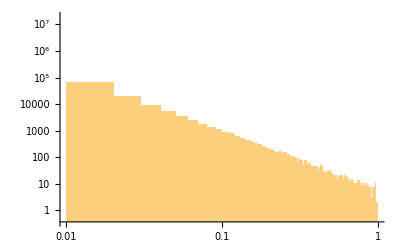

```mathematica
Histogram[dattaFullQ2[[All,-1]],100,ScalingFunctions->{"Log","Log"},PlotRange->All]
```

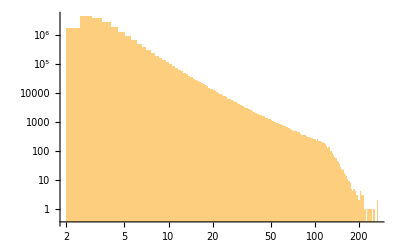

```mathematica
Histogram[mesonSample[setupSel,ptsel][[All,indexFins2]],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
4*10*100
```

4000

```mathematica
setupSel
```

100×10

```mathematica
s2maxXprod[mp,mX,me,s]
```

(√s-me)^2

#### Plots

```mathematica
labelEpilog=Row[{""}];
tttt=Select[dσdxdQ2TabEPA,NumberQ[#[[3]]]&];
labelPlotEPA=Row[{compactNameConf[setupSel],", ",ptsel," meson. EPA"}];
ptCorrEPAxy=plotDensity[tttt,True,True,True,"Q^2 [GeV^2]","x",{0.16,0.7},labelEpilog,labelPlotEPA,{10^-12.,1},{10^-4,1}];
labelPlot23=Row[{compactNameConf[setupSel],", ",ptsel," meson. 2→3"}];
ptCorr2to3x=plotDensity[pdfSimx,True,True,True,"Q^2 [GeV^2]","x",{0.16,0.35},labelEpilog,labelPlot23,{10^-12.,1},{10^-4,1}];
ptCorr2to3y=plotDensity[pdfSimy,True,True,True,"Q^2 [GeV^2]","y",{0.16,0.35},labelEpilog,labelPlot23,{10^-12.,1},{10^-4,1}];
Style[Row[{ptCorrEPAxy,ptCorr2to3y}],ImageSizeMultipliers->{1, 1}]
ptCorrEPAxyQ2window=plotDensity[Select[tttt,10^-4<#[[1]]<1.&],True,True,True,"Q^2 [GeV^2]","y",{0.13,0.7},labelEpilog,labelPlotEPA,{10^-4.,1},{3.5*10^-4,1},(*"d^2/dQ^2"*)"f"];
ptCorr2to3xQ2window=plotDensity[Select[pdfSimx,10^-4<#[[1]]<1.&],True,True,True,"Q^2 [GeV^2]","x",{0.13,0.7},labelEpilog,labelPlot23,{10^-4.,1},{3.5*10^-4,1}];
ptCorr2to3yQ2window=plotDensity[Select[pdfSimy,10^-4<#[[1]]<1.&],True,True,True,"Q^2 [GeV^2]","y",{0.13,0.7},labelEpilog,labelPlot23,{10^-4.,1},{3.5*10^-4,1},(*"d^2/dQ^2"*)"f"];
Style[Row[{ptCorrEPAxyQ2window,ptCorr2to3yQ2window}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{dir["plots"],"y-Q2-correlation-EPA.png"}],ptCorrEPAxyQ2window,ImageResolution->500]
Export[FileNameJoin[{dir["plots"],"y-Q2-correlation-2-to-3.png"}],ptCorr2to3yQ2window,ImageResolution->500]
```

-Graphics--Graphics-

-Graphics--Graphics-

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\y-Q2-correlation-EPA.png

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\y-Q2-correlation-2-to-3.png

```mathematica
4^2/(4*5^2.)
```

0.16

```mathematica
1-9.95/10.
```

0.005

### Comparison of the total cross-sections

```mathematica
mesonsP
```

{π^0,η,η'}

```mathematica
ResourceFunction["MonitorProgress"]@Do[
ResourceFunction["MonitorProgress"]@Do[
Block[{Epv=energies[setup][[1]],Eev=energies[setup][[2]],Q2max},tab=ParallelTable[{10^x,dσdQ2EPA[10^x,Eev,Epv,ptsel]//Quiet},{x,Log10[Q2minEPAabs[mP[ptsel],mpval,meval,Epv,Eev]],Log10[Q2maxEPAabs],(Log10[Q2maxEPAabs]-Log10[Q2minEPAabs[mP[ptsel],mpval,meval,Epv,Eev]])/130}];
dσdQ2int[Q2_]=If[Q2minEPAabs[mP[ptsel],mpval,meval,Epv,Eev]<=Q2<=Q2maxEPAabs,Evaluate[Interpolation[({#[[1]],#[[2]]+10^-90.}&/@tab)//Log,InterpolationOrder->1][Log[Q2]]//Exp],0.];
σtotEPA[ptsel,setup]=NIntegrate[dσdQ2int[Exp[Q2]]*Exp[Q2],{Q2,Log[Q2minEPAabs[mP[ptsel],mpval,meval,Epv,Eev]],Log[-t1thresholdRegge]},Method->"InterpolationPointsSubdivision"];
σtotEPAcut[ptsel,setup]=NIntegrate[dσdQ2int[Exp[Q2]]*Exp[Q2],{Q2,Log[1.],Log[-t1thresholdRegge]},Method->"InterpolationPointsSubdivision"]//Quiet;
dσdQ2int[Q2_]=If[Min[dσdQ22to3analytic[setup,ptsel][[All,1]]]<Q2<Max[dσdQ22to3analytic[setup,ptsel][[All,1]]],Evaluate[Interpolation[({#[[1]],#[[2]]+10^-90.}&/@dσdQ22to3analytic[setup,ptsel])//Log,InterpolationOrder->1][Log[Q2]]//Exp],0.];
σtot2to3Cut[ptsel,setup]=NIntegrate[dσdQ2int[Exp[Q2]]*Exp[Q2],{Q2,Log[1.],Log[-t1thresholdRegge]},Method->"InterpolationPointsSubdivision"]//Quiet;
]
,{setup,energylist}]
,{ptsel,mesonsP}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Q2 near {Q2} = {-24.3425}. NIntegrate obtained 8.36799×10^-7 and 3.89778×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Q2 near {Q2} = {-8.94223}. NIntegrate obtained 7.51083×10^-7 and 5.80475×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Q2 near {Q2} = {-8.48587}. NIntegrate obtained 6.66319×10^-7 and 4.89292×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Join[{{"Setup","Meson","σ_(tot, 2 → 3) [fb]","σ_(tot, EPA) [fb]","σ_(Q^2) [fb]","σ_(Q^2) [fb]"}},Flatten[Table[{setup,ptsel,btofb*σ2to3Total[setup,ptsel],btofb*σtotEPA[ptsel,setup],btofb*σtot2to3Cut[ptsel,setup],btofb*σtotEPAcut[ptsel,setup]},{setup,energylist},{ptsel,mesonsP}],1]]
```

(Setup | Meson | σ_(tot, 2 → 3) [fb] | σ_(tot, EPA) [fb] | σ_(Q^2) [fb] | σ_(Q^2) [fb]
275×18 | π^0 | 8.46377×10^8 | 8.36799×10^8 | 735424. | 2.08548×10^6
275×18 | η | 1.26173×10^8 | 1.2345×10^8 | 140005. | 318037.
275×18 | η' | 3.36683×10^7 | 3.32837×10^7 | 43337.5 | 89289.7
100×10 | π^0 | 7.6228×10^8 | 7.51083×10^8 | 735365. | 2.07271×10^6
100×10 | η | 1.13187×10^8 | 1.10231×10^8 | 139785. | 319362.
100×10 | η' | 3.0271×10^7 | 2.9469×10^7 | 43165.5 | 88590.1
41×5 | π^0 | 6.76023×10^8 | 6.66319×10^8 | 731266. | 2.06791×10^6
41×5 | η | 9.9524×10^7 | 9.69451×10^7 | 138547. | 316700.
41×5 | η' | 2.64266×10^7 | 2.56249×10^7 | 42538.8 | 87935.2)

(Setup | Meson | σ_(tot, 2 → 3) [fb] | σ_(tot, EPA) [fb] | σ_(Q^2) [fb] | σ_(Q^2) [fb]
275×18 | π^0 | 8.44444×10^8 | 8.35959×10^8 | 735424. | 2.06702×10^6
275×18 | η | 1.26099×10^8 | 1.23601×10^8 | 140005. | 320057.
275×18 | η' | 3.40807×10^7 | 3.32234×10^7 | 43337.5 | 89092.4
100×10 | π^0 | 7.60779×10^8 | 7.51528×10^8 | 735365. | 2.06337×10^6
100×10 | η | 1.13347×10^8 | 1.10217×10^8 | 139785. | 321705.
100×10 | η' | 3.03608×10^7 | 2.94622×10^7 | 43165.5 | 89088.6
41×5 | π^0 | 6.80078×10^8 | 6.66536×10^8 | 731266. | 2.07925×10^6
41×5 | η | 9.95553×10^7 | 9.6889×10^7 | 138547. | 319594.
41×5 | η' | 2.641×10^7 | 2.56179×10^7 | 42538.8 | 88885.1)

## Production of vector particles

## Calculating squared matrix elements

### Pseudoscalar

```mathematica
JvecHadrP=I*gγπV*2*gπNN*LeviCivita[μ,ν,α,β]*polV[ν]*momγ[α]*momV[β]*(ubarppr.GA5.up)*Rπ//ExpandScalarProduct//Contract;
ruleVprodP={Rπ->RπStar};
MepToepVP=JvecHadrP*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MsquaredVprodPhotoP[s_,αEM_,cosθ_,mp_,mX_,gγπV_,gπNN_,Rπ_,RπStar_]=MsquaredPhotoXInsertedKinematics[MepToepVP,MepToepVP,True,ruleVprodP];
```

### Scalar

```mathematica
JvecHadrS=√(4Pi*αEM)*gσNN*gσVγ*(momγ[κ]*momV[κ]*polV[μ]-polV[κ]*momγ[κ]*momV[μ])*(ubarppr.up)*Rσ//ExpandScalarProduct//Contract//ExpandScalarProduct//Simplify;
ruleVprodS={Rσ->RσStar};
MepToepVS=JvecHadrS*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MsquaredVprodPhotoS[s_,αEM_,cosθ_,mp_,mX_,gσNN_,gσVγ_,Rσ_,RσStar_]=MsquaredPhotoXInsertedKinematics[MepToepVS,MepToepVS,True,ruleVprodS]
```

(π αEM gσNN^2 gσVγ^2 Rσ RσStar (mp^2-s)^2 (-mp^2-cosθ √(mp^4-2 mp^2 (mX^2+s)+(mX^2-s)^2)+mX^2+s)^2 (mp^2+((mp^2+s) (mp^2-mX^2+s)+cosθ (mp^2-s) √(mp^4-2 mp^2 (mX^2+s)+(mX^2-s)^2))/(4 s)))/(2 s^2)

### Tensor

#### Vertices

```mathematica
Γf2NN[λ_,σ_,mp_]=2 gf2NN/mp*1/2(FV[pp+pppr,λ]*GA[σ]+FV[pp+pppr,σ]*GA[λ]);
structFull[μ_,ν_,α_,β_,p_,q_,mρ_]=((ScalarProduct[p,q]+mρ^2)*MT[μ,α]*MT[ν,β]+FV[p,μ]*FV[q,ν]*MT[α,β]-FV[p,μ]*FV[q,α]*MT[ν,β]-FV[p,β]*FV[q,ν]*MT[μ,α])-MT[μ,ν]*1/2*((ScalarProduct[p,q]+mρ^2)*MT[α,β]-FV[p,β]*FV[q,α]);
Γf2Vγ[gf2Vγ_,μ_,β_,ρ_]=gf2Vγ*(structFull[β,ρ,μ,κ,pγ,pX,0]*PolarizationVector[pX,κ])//ExpandScalarProduct//Contract//ExpandScalarProduct
momγ[μ]*Γf2Vγ[gf2Vγ,μ,ρ,σ]//Contract//ExpandScalarProduct//Simplify
```

-gf2Vγ OverBar[pX]^ρ (ḡ)^βμ (OverBar[pγ]·ε̄(pX))-1/2 gf2Vγ (ḡ)^βρ (ε̄)^μ(pX) (OverBar[pX]·OverBar[pγ])+gf2Vγ (ḡ)^βμ (ε̄)^ρ(pX) (OverBar[pX]·OverBar[pγ])+1/2 gf2Vγ OverBar[pX]^μ (ḡ)^βρ (OverBar[pγ]·ε̄(pX))+gf2Vγ OverBar[pγ]^β OverBar[pX]^ρ (ε̄)^μ(pX)-gf2Vγ OverBar[pγ]^β OverBar[pX]^μ (ε̄)^ρ(pX)

0

#### Squared matrix element

```mathematica
JvecHadrT=Γf2Vγ[gf2Vγ,μ,β,ρ]*PolarizationSum[λ,σ,β,ρ,pp-pppr,mf2]*(ubarppr.Γf2NN[λ,σ,mp].up)*Rf2//ExpandScalarProduct//Contract//ExpandScalarProduct//Simplify;
ruleVprodT={Rf2->Rf2Star};
MepToepVT=JvecHadrT*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MsquaredVprodPhotoT[s_,αEM_,cosθ_,mp_,mX_,gf2NN_,gf2Vγ_,mf2_,Rf2_,Rf2Star_]=MsquaredPhotoXInsertedKinematics[MepToepVT,MepToepVT,True,ruleVprodT];//AbsoluteTiming
```

{43.535,Null}

### Pomeron

```mathematica
JvecHadrPomeron=12*I*√(4Pi*αEM)ββtoF*FPomeron*(ubarppr.(GA[κ]*momγ[κ]*polV[μ]-GA[μ]*polV[κ]*momγ[κ]).up)*RPomeron//ExpandScalarProduct//Contract//ExpandScalarProduct//Simplify;
ruleVprodPomeron={RPomeron->RPomeronStar};
MepToepVPomeron=JvecHadrPomeron*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MsquaredVprodPhotoPomeron[s_,αEM_,cosθ_,mp_,mX_,ββtoF_,FPomeron_,RPomeron_,RPomeronStar_]=MsquaredPhotoXInsertedKinematics[MepToepVPomeron,MepToepVPomeron,True,ruleVprodPomeron];
```

### Nucleon resonances (toy)

#### v1

```mathematica
(*FbaryonicExplicit[s_]=With[{ΛB=1.5,mB=1.3},If[s<3.1,2 √2,2 √2(s/3.1)^-0.75]];

JvecHadrN1=Fbaryonic*ReggeNs*(√(4Pi*αEM))^2*gVNN*1/(ScalarProduct[pp+pγ,pp+pγ]-mp^2)ubarppr.GA[ν].(GS[pp+pγ]+mp).GA[μ].up*polV[ν]//Contract
JvecHadrN2=Fbaryonic*ReggeNu*(√(4Pi*αEM))^2*gVNN*1/(ScalarProduct[pp-pX,pp-pX]-mp^2)ubarppr.GA[μ].(GS[pp-pX]+mp).GA[ν].up*polV[ν]//Contract;
MepToepVN=(JvecHadrN1+JvecHadrN2)*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
ruleVprodN={ReggeNs->ReggeNsStar,ReggeNu->ReggeNuStar};
MsquaredVprodPhotoN[s_,αEM_,cosθ_,mp_,mX_,gVNN_,Fbaryonic_,ReggeNs_,ReggeNu_]=MsquaredPhotoXInsertedKinematics[MepToepVN,MepToepVN,{}];*)

With[{ps=pp+pγ,pu=pp-pX,Fhat=(*ReggeNs+ReggeNu-ReggeNs*ReggeNu*)0},
If[Fhat===0,
gaugePieceN1=gaugePieceN2=0;
,
gaugePieceN1=-FV[2*pp+pγ,μ]/(ScalarProduct[ps,ps]-mp^2)*(ReggeNs-Fhat)/ReggeNs*(ubarppr.GA[ν].up)*polV[ν]//Contract;
gaugePieceN2=-FV[2*pppr-pγ,μ]/(ScalarProduct[pu,pu]-mp^2)*(ReggeNu-Fhat)/ReggeNu*(ubarppr.GA[ν].up)*polV[ν]//Contract;
];
JvecHadrN1=Fbaryonic*ReggeNs*(Sqrt[4 Pi*αEM])^2*gVNN*((ubarppr.GA[ν].(GS[ps]+mp).GA[μ].up)*polV[ν]/(ScalarProduct[ps,ps]-mp^2)+gaugePieceN1)//Contract//Simplify;
JvecHadrN2=Fbaryonic*ReggeNu*(Sqrt[4 Pi*αEM])^2*gVNN*((ubarppr.GA[μ].(GS[pu]+mp).GA[ν].up)*polV[ν]/(ScalarProduct[pu,pu]-mp^2)+gaugePieceN2)//Contract//Simplify;
];
MepToepVN1=(JvecHadrN1)*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MepToepVN2=(JvecHadrN2)*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MepToepVN=MepToepVN1+MepToepVN2;
ruleVprodN={ReggeNs->ReggeNsStar,ReggeNu->ReggeNuStar};
MsquaredVprodPhotoN[s_,αEM_,cosθ_,mp_,mX_,gVNN_,Fbaryonic_,ReggeNs_,ReggeNsStar_,ReggeNu_,ReggeNuStar_]=MsquaredPhotoXInsertedKinematics[MepToepVN1,MepToepVN1,True,ruleVprodN]+MsquaredPhotoXInsertedKinematics[MepToepVN2,MepToepVN2,True,ruleVprodN]+MsquaredPhotoXInsertedKinematics[MepToepVN1,MepToepVN2,True,ruleVprodN,ruleVprodN];//AbsoluteTiming
With[{MepToepVN=(JvecHadrN1+JvecHadrN2)*FV[pγ,μ]*PolarizationVector[pγ,κ]//ExpandScalarProduct//Contract//Simplify},
(MsquaredPhotoXInsertedKinematics[MepToepVN,MepToepVN,True,ruleVprodN]/.{ReggeNs->ReggeNu,ReggeNsStar->ReggeNuStar})===0
]
(*ReggeNS[s_,Λs_,mB_]=Λs^4/(Λs^4+(s-mB^2)^2);
ReggeNU[s_,t_,mX_,Λu_,mB_]=(Λu^4/(Λu^4+(ScalarProduct[pp-pX,pp-pX]-mB^2)^2)//ExpandScalarProduct)/.scalarProductsRepl2to2/.{mp->mpval,cosθ->cosθCMt[s,mpval,mX,t]}//Simplify;*)
```

{1.65964,Null}

True

#### v2

```mathematica
(*With[{ps=pp+pγ,pu=pp-pX,Fhat=(*ReggeNs+ReggeNu-ReggeNs*ReggeNu*)0},
gaugePieceN1=-(FV[2*pp+pγ,μ]/(ScalarProduct[ps,ps]-mp^2))*(ubarppr.GA[ν].up)*polV[ν]//Contract//Simplify;
gaugePieceN2=-(FV[2*pppr-pγ,μ]/(ScalarProduct[pu,pu]-mp^2))*(ubarppr.GA[ν].up)*polV[ν]//Contract//Simplify;
JvecHadrN1=Fbaryonic*(Sqrt[4 Pi*αEM])^2*gVNN*((ubarppr.GA[ν].(GS[ps]+mp).GA[μ].up)*polV[ν]/(ScalarProduct[ps,ps]-mp^2)+gaugePieceN1)//Contract//Simplify;
JvecHadrN2=Fbaryonic*(Sqrt[4 Pi*αEM])^2*gVNN*((ubarppr.GA[μ].(GS[pu]+mp).GA[ν].up)*polV[ν]/(ScalarProduct[pu,pu]-mp^2)+gaugePieceN2)//Contract//Simplify;
MepToepVN1=(JvecHadrN1)*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
MepToepVN2=(JvecHadrN2)*polγ[μ]//ExpandScalarProduct//Contract//Simplify;
(*Reggeizing*)
MepToepVN1*=(ScalarProduct[pu,pu]-mp^2)*ReggeNs;
MepToepVN2*=(ScalarProduct[pu,pu]-mp^2)*ReggeNs;
MepToepVN=MepToepVN1+MepToepVN2;
];
ruleVprodN={ReggeNs->ReggeNsStar,ReggeNu->ReggeNuStar};
MsquaredVprodPhotoN[s_,αEM_,cosθ_,mp_,mX_,gVNN_,Fbaryonic_,ReggeNs_,ReggeNsStar_,ReggeNu_,ReggeNuStar_]=MsquaredPhotoXInsertedKinematics[MepToepVN1,MepToepVN1,ruleVprodN]+MsquaredPhotoXInsertedKinematics[MepToepVN2,MepToepVN2,ruleVprodN]+MsquaredPhotoXInsertedKinematics[MepToepVN1,MepToepVN2,ruleVprodN,ruleVprodN];//AbsoluteTiming
With[{MepToepVN=(JvecHadrN1+JvecHadrN2)*FV[pγ,μ]*PolarizationVector[pγ,κ]//ExpandScalarProduct//Contract//Simplify},
MsquaredPhotoXInsertedKinematics[MepToepVN,MepToepVN,ruleVprodN]==0]
(*Reggeized propagator*)
ReggeizedNucleon[s_,t_,mX_]=-αNpr*Gamma[1/2-αN]*(1+Exp[-I*Pi*(αN-1/2)])/2 s^(αN-1/2)/.{αN->αNpr*u+α0}/.{u->ExpandScalarProduct[ScalarProduct[pp-pX,pp-pX]]}/.scalarProductsRepl2to2/.{cosθ->cosθCMt[s,mp,mX,t]}/.{αNpr->0.9,α0->-0.365,mp->mpval};
ReggeizedNucleonStar[s_,t_,mX_]=-αNpr*Gamma[1/2-αN]*(1+Exp[+I*Pi*(αN-1/2)])/2 s^(αN-1/2)/.{αN->αNpr*u+α0}/.{u->ExpandScalarProduct[ScalarProduct[pp-pX,pp-pX]]}/.scalarProductsRepl2to2/.{cosθ->cosθCMt[s,mp,mX,t]}/.{αNpr->0.9,α0->-0.365,mp->mpval};*)
```

### Interference

```mathematica
(*factorToy=2.4;*)
tmp=MsquaredPhotoXInsertedKinematics[MepToepVP,MepToepVS,True,ruleVprodP,ruleVprodS]+MsquaredPhotoXInsertedKinematics[MepToepVP,MepToepVPomeron,True,ruleVprodP,ruleVprodPomeron]+MsquaredPhotoXInsertedKinematics[MepToepVP,MepToepVT,True,ruleVprodP,ruleVprodT]+MsquaredPhotoXInsertedKinematics[MepToepVP,MepToepVN,True,ruleVprodP,ruleVprodN];//AbsoluteTiming
tmp+=MsquaredPhotoXInsertedKinematics[MepToepVS,MepToepVT,True,ruleVprodS,ruleVprodT]+MsquaredPhotoXInsertedKinematics[MepToepVS,MepToepVPomeron,True,ruleVprodS,ruleVprodPomeron]+MsquaredPhotoXInsertedKinematics[MepToepVS,MepToepVN,True,ruleVprodS,ruleVprodN];//AbsoluteTiming
tmp+=MsquaredPhotoXInsertedKinematics[MepToepVPomeron,MepToepVT,True,ruleVprodPomeron,ruleVprodT]+Simplify[MsquaredPhotoXInsertedKinematics[MepToepVPomeron,MepToepVN,True,ruleVprodPomeron,ruleVprodN]];//AbsoluteTiming
tmp+=MsquaredPhotoXInsertedKinematics[MepToepVT,MepToepVN,True,ruleVprodT,ruleVprodN];//AbsoluteTiming
MsquaredVprodPhotoInterference[s_,αEM_,cosθ_,mp_,mX_,gγπV_,gπNN_,Rπ_,RπStar_,gσNN_,gσVγ_,Rσ_,RσStar_,gf2NN_,gf2Vγ_,mf2_,Rf2_,Rf2Star_,ββtoF_,FPomeron_,RPomeron_,RPomeronStar_,Fbaryonic_,ReggeNs_,ReggeNsStar_,ReggeNu_,ReggeNuStar_]=tmp;
tmp//Clear
```

{2.30952,Null}

{5.33872,Null}

{6.35249,Null}

{22.3079,Null}

## Differential cross-section (numeric)

### Error bars

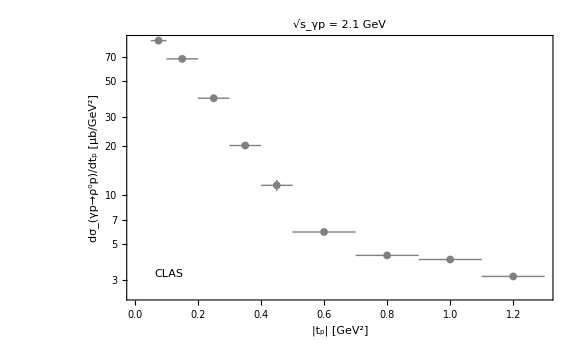

```mathematica
errorBars//Clear
errorBars["ρ^0",1.5]={{Around[0.075,0.025],Around[78,0]},{Around[0.15,0.05],Around[61,0]},{Around[0.25,0.05],Around[35,0]},{Around[0.35,0.05],Around[14,0]},{Around[0.45,0.05],Around[8,0.9]},{Around[0.6,0.1],Around[7.4,0]},{Around[0.8,0.1],Around[6.75,0]},{Around[1.,0.1],Around[6.33,0]},{Around[1.2,0.1],Around[5.,0.7]}};
expErrors["ρ^0",1.5]="CLAS";
errorBars["ρ^0",1.9]={{Around[0.075,0.025],Around[88,0]},{Around[0.15,0.05],Around[68,0]},{Around[0.25,0.05],Around[39,0]},{Around[0.35,0.05],Around[20,0]},{Around[0.45,0.05],Around[11.4,0.9]},{Around[0.6,0.1],Around[5.9,0]},{Around[0.8,0.1],Around[4.24,0]},{Around[1.,0.1],Around[4,0]},{Around[1.2,0.1],Around[3.15,0.]}};
expErrors["ρ^0",1.9]="CLAS";
errorBars["ρ^0",2.5]={{Around[0.075,0.025],Around[52,9]},{Around[0.15,0.05],Around[47,0]},{Around[0.25,0.05],Around[30,0]},{Around[0.35,0.05],Around[15.6,0]},{Around[0.45,0.05],Around[9.5,0.9]},{Around[0.6,0.1],Around[5.4,0]},{Around[0.8,0.1],Around[2.8,0]},{Around[1.,0.1],Around[2.4,0]},{Around[1.2,0.1],Around[2.2,0.]}};
expErrors["ρ^0",2.5]="CLAS";
errorBars["ρ^0",2.8]={{Around[0.035,0.015],Around[115,0]},{Around[0.065,0.015],Around[87,0]},{Around[0.09,0.01],Around[67,0]},{Around[0.125,0.02],Around[55,0]},{Around[0.175,0.025],Around[36,6]},{Around[0.225,0.025],Around[29,4]},{Around[0.27,0.025],Around[19,4]},{Around[0.325,0.025],Around[15,4]},{Around[0.375,0.025],Around[7.6,2.4]},{Around[0.45,0.05],Around[4.7,1.8]},{Around[0.6,0.1],Around[3.2,0.8]},{Around[0.85,0.15],Around[1,0.65]},{Around[1.25,0.25],Around[0.7,0.45]}};
expErrors["ρ^0",2.8]="CLAS";
errorBars["ρ^0",3.82]={{Around[0.15,0.01],Around[39,0]},{Around[0.25,0.01],Around[25,0]},{Around[0.35,0.01],Around[13.1,0]},{Around[0.625,0.01],Around[2.2,0.3]},{Around[0.875,0.01],Around[0.77,0.1]},{Around[1.125,0.01],Around[0.39,0.06]},{Around[1.4,0.01],Around[0.26,0.06]},{Around[1.75,0.01],Around[0.094,0.03]},{Around[2.25,0.01],Around[0.057,0.022]},{Around[2.75,0.01],Around[0.042,0.01]},{Around[3.25,0.01],Around[0.027,0.01]},{Around[3.75,0.01],Around[0.032,0.012]},{Around[4.25,0.01],Around[0.04,0.01]},{Around[4.75,0.01],Around[0.049,0.01]}};
expErrors["ρ^0",3.82]="SAPHIR";
errorBars["ρ^0",4.7]={{Around[0.03,0.015],Around[82.9,0]},{Around[0.055,0.01],Around[65.7,0]},{Around[0.08,0.015],Around[52,0]},{Around[0.12,0.025],Around[43.9,0]},{Around[0.17,0.025],Around[35.8,4]},{Around[0.22,0.025],Around[15.5,3.5]},{Around[0.27,0.025],Around[12.8,3.2]},{Around[0.32,0.025],Around[8.9,2.5]},{Around[0.37,0.025],Around[6.7,2]},{Around[0.445,0.05],Around[5.3,1.2]},{Around[0.6,0.1],Around[0.59,0.5]},{Around[0.85,0.15],Around[0.9,0.3]},{Around[1.25,0.25],Around[0.15,0.17]}};
expErrors["ρ^0",4.7]="SLAC";
keysErrorBars=Keys[DownValues@errorBars][[All,1,#]]&/@{1,2}//Transpose;
plotErrorBarsSimple[meson_,Eγ_,color_]:=Module[{},
ListLogPlot[errorBars[meson,Eγ],PlotStyle->{{Thick,color}},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],FrameLabel->{"|t_p| [GeV^2]",Row[{Subscript["dσ","γp→"<>meson<>"p"],"/dt_p [μb/GeV^2]"}]}]
]
errorBarLegendMarker[color_]:=Graphics[{Directive[color,AbsoluteThickness[1.8]],(*vertical error bar*)Line[{{0.5,0.18},{0.5,0.82}}],Line[{{0.38,0.18},{0.62,0.18}}],Line[{{0.38,0.82},{0.62,0.82}}],(*horizontal error bar*)Line[{{0.18,0.5},{0.82,0.5}}],Line[{{0.18,0.38},{0.18,0.62}}],Line[{{0.82,0.38},{0.82,0.62}}],(*central point*)PointSize[0.16],Point[{0.5,0.5}]},PlotRange->{{0,1},{0,1}},ImageSize->18,Background->None];

errorBarLegend[label_,color_]:=Row[{errorBarLegendMarker[color],Spacer[6],Style[label,16,Black,FontFamily->"Palatino"]}];
plotErrorBars[meson_,Eγ_,color_,ptrangex_:Automatic,ptrangey_:Automatic,legendplac_:{0.1,0.1}]:=Module[{lbl=expErrors[meson,Eγ]},Show[ListLogPlot[errorBars[meson,Eγ],PlotStyle->Directive[Thick,color],PlotMarkers->{Automatic,8},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotRange->{ptrangex,ptrangey},FrameLabel->{"|t_p| [GeV^2]",Row[{Subscript["dσ","γp→"<>meson<>"p"],"/dt_p [μb/GeV^2]"}]},PlotLabel->Style[Row[{"√s_γp = ",Round[√(mpval^2+2*mpval*Eγ),0.1],"  GeV"}],20,Black,FontFamily->"Palatino"],ImagePadding->{{Automatic, Automatic}, {Automatic, 0.6}}],Epilog->Inset[errorBarLegend[lbl,color],Scaled[legendplac]]]];
plotErrorBars["ρ^0",1.9,Gray,Automatic,Automatic,{0.1,0.1}]
```

### Finding fit to the nucleon matrix element

(3.61 | 2.5 | 2.5 | 0.308085
4.07232 | 1.8 | 1.8 | 0.185103
4.44788 | 1.02 | 1.05 | 0.14231
4.82242 | 0.8 | 1. | 0.115493
5.1984 | 0.4 | 0.9 | 0.0963752
5.5696 | 0.25 | 0.8 | 0.0820837
6.13553 | 0.12 | 0.15 | 0.0658655
7.0331 | 0.043 | 0.043 | 0.0485538
7.54052 | 0.025 | 0.03 | 0.0416266
8.04857 | 0.015 | 0.018 | 0.0360699
10.9892 | 0.0034 | 0.0034 | 0.0183582)

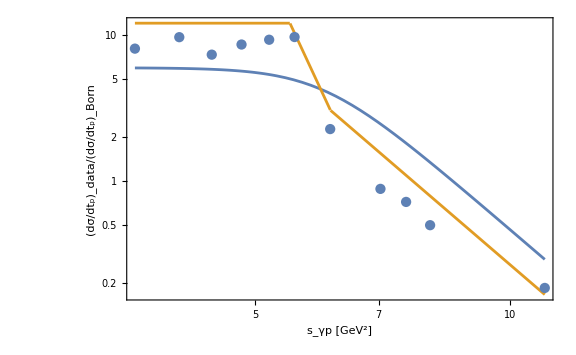

```mathematica
replNumPhotoV[V_]:={mp->mpval,mX->MASS[V],mf2->MASS["f_2(1270)"],αEM->αEMval,gσNN->gσNNval,gf2NN->gf2NN1val,gf2Vγ->gf2VγVal[V],gσVγ->gσVγVal[V],gγπV->gPVγ["π^0",V],ββtoF->ββtoFval[V],gπNN->gPNN["π^0"],gVNN->gVNNval[V]};
Do[
(*s2->s,t2->-t*)
reggeizedRepl={Fbaryonic->(*FbaryonicExplicit[s]*)1,ReggeNs->(*ReggeizedNucleon[s,t,mX]*)1,ReggeNsStar->(*ReggeizedNucleonStar[s,t,mX]*)1,ReggeNu->1,ReggeNuStar->1};
dσVproddtPhotoN[s_,t_,V]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoN[s,αEM,cosθ,mp,mX,gVNN,Fbaryonic,ReggeNu,ReggeNuStar,ReggeNs,ReggeNsStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
,{V,{"ρ^0","ω","ϕ"}}]
tabToFit={{1.9,2.5,2.5},{2.018,1.8,1.8},{2.109,1.02,1.05},{2.196,0.8,1.},{2.28,0.4,0.9},{2.36,0.25,0.8},{2.477,0.12,0.15},{2.652,0.043,0.043},{2.746,0.025,0.03},{2.837,0.015,0.018},{3.315,3.4*10^-3,3.4*10^-3}};
tabToFit={(#[[1]])^2,#[[2]],#[[3]]}&/@tabToFit;
tabToFit=With[{tseed=1.},Join[tabToFit,{GeVm2Tob*10^6*dσVproddtPhotoN[#[[1]],Min[tseed,0.9*tmax[#[[1]],mpval,MASS["ρ^0"]]],"ρ^0"]}&/@tabToFit,2]]
funcFit[s_]=1.5*(3.4/2.7)^2*If[s<=5.5,5.1,If[5.5<s<=6.14,5.1*(5.5/s)^12.5,(5.1*(5.5/6.14)^12.5)(6.14/s)^5]];
constrFunc[norm_,s1_,s2_,pow_]:=Block[{},
fit1[s_]=norm;
fit2[s_,s0v_]=(s0v/s)^pow;
fit3[s_,s1v_]=(s1v/s)^5;
s0vSol=s0v/.NSolve[fit1[s1]==fit2[s1,s0v],s0v,Reals][[1]];
s1vSol=s1v/.NSolve[fit3[s2,s1v]==fit2[s2,s0vSol],s1v,Reals][[1]];
If[s<s1,Evaluate[fit1[s]],Evaluate[If[s1<=s<s2,Evaluate[fit2[s,s0vSol]],Evaluate[fit3[s,s1vSol]]]]]
]
funcFitNew[s_]=constrFunc[12,5.6,6.1,7];
Show[LogLogPlot[{6 1/((1+(s/6)^10)^(1/2)),funcFit[s]},{s,1.9^2,3.315^2},Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],FrameLabel->{"s_γp [GeV^2]","(dσ/dt_p)_data/(dσ/dt_p)_Born"},ImageSize->Large,PlotRange->All],ListLogLogPlot[{#[[1]],(#[[3]])/(#[[4]])}&/@tabToFit]]
fitFuncExact[s_,t_]=Interpolation[{#[[1]],(#[[3]])/(#[[4]])}&/@tabToFit//Log,InterpolationOrder->1][Log[s]]//Exp;
```

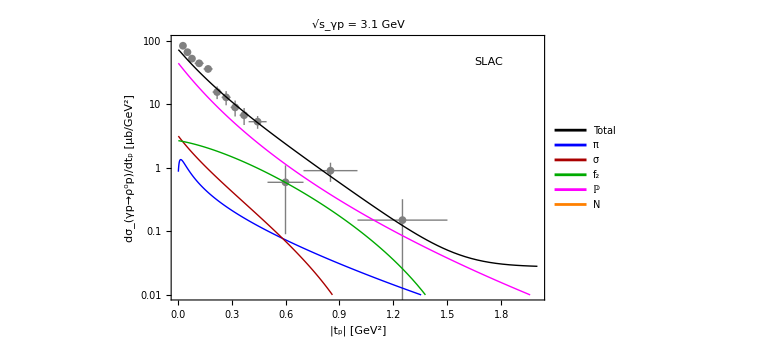

```mathematica
(*replNumPhotoV[V_]:={mp->mpval,mX->MASS[V],mf2->MASS["f_2(1270)"],αEM->αEMval,gσNN->gσNNval,gf2NN->gf2NN1val,gf2Vγ->gf2VγVal[V],gσVγ->gσVγVal[V],gγπV->gPVγ["π^0",V],ββtoF->ββtoFval[V],gπNN->gPNN["π^0"],gVNN->gVNNval[V],factorToy->2.4};
fakeFac=1.3;
phaseFactorNucl=-I;
fitFunc[s_,t_]=phaseFactorNucl*fakeFac*√funcFit[s](2/(1+s))^(0.0*t);
fitFuncC[s_,t_]=Conjugate[phaseFactorNucl]*fitFunc[s,t]/phaseFactorNucl//Simplify;
facS=Abs[1.048/gσVγVal["ρ^0"]];
*)
replNumPhotoV[V_]:={mp->mpval,mX->MASS[V],mf2->MASS["f_2(1270)"],αEM->αEMval,gσNN->gσNNval,gf2NN->gf2NN1val,gf2Vγ->gf2VγVal[V],gσVγ->gσVγVal[V],gγπV->gPVγ["π^0",V],ββtoF->ββtoFval[V],gπNN->gPNN["π^0"],gVNN->gVNNval[V]};
(*________*)
(*Temporary modification of the nucleon coupling*)
(*Nucleon couplings*)
(*________*)
fakeFac=1.;
phaseFactorNucl=1;
ReggeNU[s_,t_,mX_,Λu_,mB_]=(Λu^4/(Λu^4+(ScalarProduct[pp-pX,pp-pX]-mB^2)^2)//ExpandScalarProduct)/.scalarProductsRepl2to2/.{mp->mpval,cosθ->cosθCMt[s,mpval,mX,t]}//Simplify;
(*funcFit[s_]=constrFunc[12,5.6,6.1,14];*)
funcFitNew[s_]=constrFunc[12,6.25,6.5,11];
fitFunc[s_,t_,mX_]=phaseFactorNucl*fakeFac*√funcFit[s](*(2/(1+s))^(0.05*t)*)(*ReggeNU[s,t,MASS["ρ^0"],2.5,mpval]*)//Simplify;
fitFuncC[s_,t_,mX_]=Conjugate[phaseFactorNucl]*fitFunc[s,t,mX]/phaseFactorNucl//Simplify;
(*fitFunc[s_,t_,mX_]=10000fitFuncExact[s,t]*ReggeizedNucleon[s,t,mX];
fitFuncC[s_,t_,mX_]=10000fitFuncExact[s,t]*ReggeizedNucleonStar[s,t,mX];*)
fakeFacPomeron=1.;
(*________*)
(*Temporary modification of the scalar coupling. Allowed values are (1.01-1.39)/gσVγVal["ρ^0"]*)
(*________*)
facS=1.;
(*________*)
(*Temporary modification of the Subscript[f, 2] coupling. Allowed values are up to 0.63 GeV^-1/Subscript[g, Subscript[f, 2] Vγ]*)
(*________*)
facf2=gf2VγVal["ρ^0"]/gf2VγVal["ρ^0"];
Do[
(*s2->s,t2->-t*)
RπV[s_,t_]=If[V=="ω",Reggeizedπ0ω[s,-t],Reggeizedπ0[s,-t]];
RπStarV[s_,t_]=If[V=="ω",Reggeizedπ0ωStar[s,-t],Reggeizedπ0Star[s,-t]];
(*reggeizedRepl={Rπ->RπV[s,t],RπStar->RπStarV[s,t],Rσ->Reggeizedσ[s,-t],RσStar->ReggeizedσStar[s,-t],Rf2->Reggeizedf2[s,-t],Rf2Star->Reggeizedf2Star[s,-t],RPomeron->ReggeizedPomeron[s,-t],RPomeronStar->ReggeizedPomeronStar[s,-t],FPomeron->F1VtimesFμ0[-t,mX],Fbaryonic->(*FbaryonicExplicit[s]*)1,ReggeNs->fitFunc[s,t],ReggeNsStar->fitFuncC[s,t],ReggeNu->fitFunc[s,t],ReggeNuStar->fitFuncC[s,t]};*)
reggeizedRepl={Rπ->RπV[s,t],RπStar->RπStarV[s,t],Rσ->facS*Reggeizedσ[s,-t],RσStar->facS*ReggeizedσStar[s,-t],Rf2->facf2*Reggeizedf2[s,-t],Rf2Star->facf2*Reggeizedf2Star[s,-t],RPomeron->ReggeizedPomeron[s,-t],RPomeronStar->ReggeizedPomeronStar[s,-t],FPomeron->fakeFacPomeron*F1VtimesFμ0[-t,mX],Fbaryonic->(*FbaryonicExplicit[s]*)1,ReggeNs->fitFunc[s,t,mX],ReggeNsStar->fitFuncC[s,t,mX],ReggeNu->fitFunc[s,t,mX],ReggeNuStar->fitFuncC[s,t,mX]};
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s_,t_,V,"P"]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoP[s,αEM,cosθ,mp,mX,gγπV,gπNN,Rπ,RπStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
dσVproddtPhoto[s_,t_,V,"S"]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoS[s,αEM,cosθ,mp,mX,gσNN,gσVγ,Rσ,RσStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s,t,V]+dσVproddtPhoto[s,t,V,"S"];
dσVproddtPhoto[s_,t_,V,"T"]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoT[s,αEM,cosθ,mp,mX,gf2NN,gf2Vγ,mf2,Rf2,Rf2Star]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s,t,V]+dσVproddtPhoto[s,t,V,"T"];
dσVproddtPhoto[s_,t_,V,"Pomeron"]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoPomeron[s,αEM,cosθ,mp,mX,ββtoF,FPomeron,RPomeron,RPomeronStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s,t,V]+dσVproddtPhoto[s,t,V,"Pomeron"];
dσVproddtPhoto[s_,t_,V,"N"]=If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoN[s,αEM,cosθ,mp,mX,gVNN,Fbaryonic,ReggeNu,ReggeNuStar,ReggeNs,ReggeNsStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s,t,V]+dσVproddtPhoto[s,t,V,"N"];
dσVproddtPhoto[s_,t_,V]=dσVproddtPhoto[s,t,V]+If[tmin[s,mpval,mX]<t<tmax[s,mpval,mX],Evaluate[dσdtXphotoTemp[MsquaredVprodPhotoInterference[s,αEM,cosθ,mp,mX,gγπV,gπNN,Rπ,RπStar,gσNN,gσVγ,Rσ,RσStar,gf2NN,gf2Vγ,mf2,Rf2,Rf2Star,ββtoF,FPomeron,RPomeron,RPomeronStar,Fbaryonic,ReggeNs,ReggeNsStar,ReggeNu,ReggeNuStar]]/.reggeizedRepl],0.]/.replNumPhotoV[V];
,{V,{"ρ^0","ω","ϕ"}}]
With[{Eγ=4.7,V="ρ^0",tmaxPlot=2,ymin=10^-2.,ymax=100.,ifLeg=True},
With[{ECM=√(mpval^2+2*Eγ*mpval)},
{tmind,tmaxd}={tmin[ECM^2,mpval,MASS[V]],Min[tmax[ECM^2,mpval,MASS[V]],tmaxPlot]};
tvals=Table[10^x,{x,Log10[tmind],Log10[tmaxd],(Log10[tmaxd]-Log10[tmind])/300}];
If[ifLeg,
legs=Placed[Style[Row[{#}],20,Black,FontFamily->"Palatino"]&/@{"Total","π","σ","f_2","ℙ","N"},{0.85,0.6}];
,
legs={}
];
tabdσt={#,Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V]],Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V,"P"]],Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V,"S"]],Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V,"T"]],Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V,"Pomeron"]],Re[GeVm2Tob*10^6*dσVproddtPhoto[ECM^2,#,V,"N"]]}&/@tvals;
pt2=ListLogPlot[Evaluate[tabdσt[[All,{1,#}]]&/@Range[2,7]],PlotRange->{{tmind,tmaxd},{ymin,ymax}},Frame->True,AspectRatio->1,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"],Joined->True,PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Green},{Thick,Magenta},{Thick,Orange}},PlotLegends->legs,FrameLabel->{"|t_p| [GeV^2]","dσ/dt_p [μb/GeV^2]"},PlotLabel->Style[Row[{"γp→",V,"p. E_γ = ",Eγ," GeV, √s_γp = ",Round[ECM,0.1]," GeV"}],15,Black,FontFamily->"Palatino"],ImagePadding->{{Automatic,Automatic}, {Automatic, 0.6}}];
If[MemberQ[keysErrorBars,{V,Eγ}],
If[ifLeg,placerr={0.85,0.9},placerr={0.85,0.9}];
pt0=plotErrorBars[V,Eγ,Gray,{tmind,tmaxd},{ymin,ymax}];
ptfin=Show[plotErrorBars[V,Eγ,Gray,{tmind,tmaxd},{ymin,ymax},placerr],pt2];
,
ptfin=pt2;
]
];
Export[FileNameJoin[{dir["plots"],"diffSigmaRho-Egamma="<>ToString[Eγ]<>"-GeV.pdf"}],ptfin];
ptfin
]
```

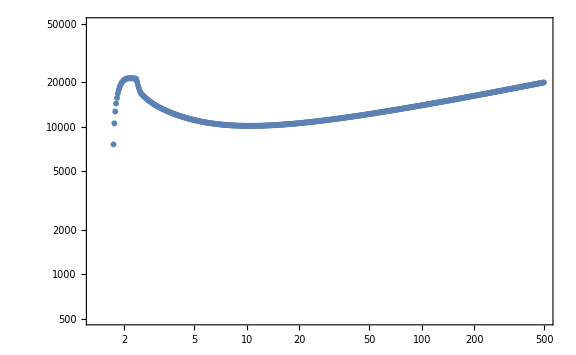

```mathematica
σWtab=Module[{mes="ρ^0"},
ParallelTable[
If[ECM>mpval+MASS[mes],
Module[{tmind,tmaxd,tvals,tabdσt,intt},
{tmind,tmaxd}={tmin[ECM^2,mpval,MASS[mes]],tmax[ECM^2,mpval,MASS[mes]]};
tvals=Table[10^x,{x,Log10[tmind],Log10[tmaxd],(Log10[tmaxd]-Log10[tmind])/300}];
tabdσt=
{#,Max[10^-90.,Quiet[Re[GeVm2Tob*10^9*dσVproddtPhoto[ECM^2,#,mes]]]]}&/@tvals;
intt[t_]=Interpolation[tabdσt[[All,{1,2}]]//Log,InterpolationOrder->1][Log[t]]//Exp;
Quiet[{ECM,Quiet[NIntegrate[intt[Exp[t]]Exp[t],{t,Log[tmind],Log[tmaxd]}]]}]
]
,
{ECM,0.}
]
,{ECM,Table[10^x,{x,Log10[mpval+MASS[mes]],Log10[500.],0.005}]}]
];
ListLogLogPlot[σWtab,PlotRange->{All,{500,5*10^4}},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20,FontFamily->"Palatino"]]
```

1.3125

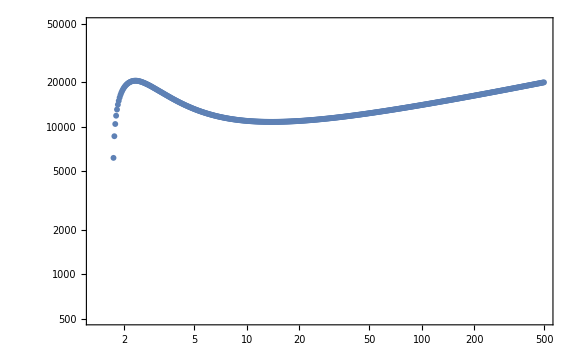

```mathematica
2.1/1.6
```

## Calculating differential cross-sections